```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Study number of junctions supported by ≥ K samples*)
```

```mathematica
aggregatedJunctionCounts=Drop[Import["hg19.sample.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];annotatedJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,3}]]];exonSkipJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,4}]]];altStartEndJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,5}]]];
novelJunctions=exonSkips=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
```

```mathematica
exonSkipAnnotatedJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]}];
someEvidenceJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]+altStartEndJunctions[[All,2]]}];
```

```mathematica
mathematicaColors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Introduce levels of evidence, and annotated with junction counts for ≥ 1000 samples*)
```

```mathematica
labelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.033],Bold,TextAlignment->Left], y]
```

```mathematica
idx=16446-999
```

15447

```mathematica
bigLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.055],Bold,TextAlignment->Right], y]
```

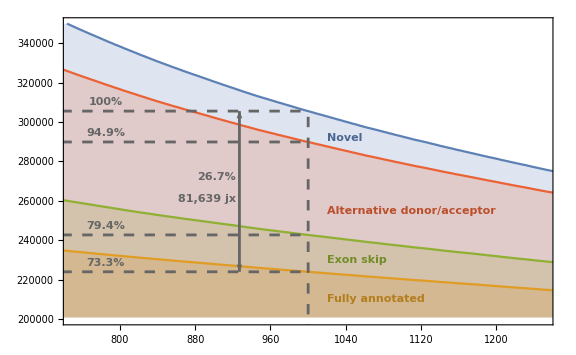

```mathematica
dashedColor=Darker[Gray,0.2];numberStartPos=785;insetAnnotationPlot=Show[ListPlot[{totalJunctions,annotatedJunctions,exonSkipAnnotatedJunctions, someEvidenceJunctions}, Joined->True, PlotRange->{{750, 1250},{200000,350000}}, Filling->Axis,  Frame->True,ImageSize->Large, BaseStyle->{FontFamily->"Arial",FontSize->15}], Graphics[{Directive[Thickness[0.0035],Dashing[0.013], dashedColor],Line[{{1000,0},totalJunctions[[idx]]}],Line[{{0,totalJunctions[[idx]][[2]]},totalJunctions[[idx]]}],Line[{{0,annotatedJunctions[[idx]][[2]]},annotatedJunctions[[idx]]}],
Line[{{0,exonSkipAnnotatedJunctions[[idx]][[2]]},exonSkipAnnotatedJunctions[[idx]]}],Line[{{0,someEvidenceJunctions[[idx]][[2]]},someEvidenceJunctions[[idx]]}],Directive[{Dashing[None],Arrowheads[{-.05,.05}]}], Arrow[{{927,annotatedJunctions[[idx]][[2]]},{927,totalJunctions[[idx]][[2]]}}],bigLabelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%",{923, 272000}, {1,0}],labelForm[ToString[NumberForm[totalJunctions[[idx,2]]-annotatedJunctions[[idx,2]],DigitBlock->3]]<>" jx", {923, 261000},{1,0}],labelForm["100%",{numberStartPos,totalJunctions[[idx]][[2]]+4500}],labelForm[ToString[NumberForm[N[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,someEvidenceJunctions[[idx]][[2]]+4500}],
labelForm[ToString[NumberForm[N[annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,annotatedJunctions[[idx]][[2]]+4500}],
labelForm[ToString[NumberForm[N[exonSkipAnnotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,exonSkipAnnotatedJunctions[[idx]][[2]]+4500}],(*Directive[Thickness[0.0035],Arrowheads[.035],Dashing[None], dashedColor],Arrow[{{1000,totalJunctions[[idx]][[2]]+41000},{1000,totalJunctions[[idx]][[2]]+100}}],labelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100],3]]<>"% of jx unannotated, but\n"<>ToString[NumberForm[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100//N,3]]<>"% of jx have donor and/or\nacceptor site in annotation", {1005, 330000}, {-1,0}],*)Darker[mathematicaColors[[1]], 0.2],labelForm["Novel",{1020,292000}, {-1,0}],Darker[mathematicaColors[[4]], 0.2],labelForm["Alternative donor/acceptor",{1020,255000}, {-1,0}],Darker[mathematicaColors[[3]], 0.2],labelForm["Exon skip",{1020,230000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2],labelForm["Fully annotated",{1020,210000}, {-1,0}]}]]
```

```mathematica
baseImageSize={576,408}*1.3
```

{748.8,530.4}

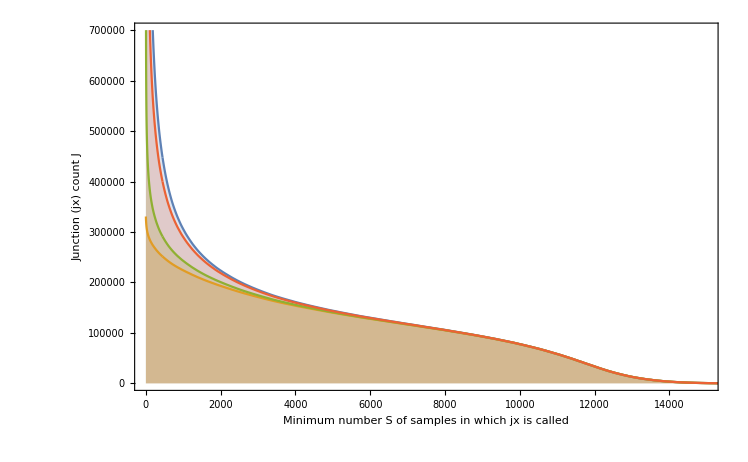

```mathematica
bigAnnotationPlot=ListPlot[{totalJunctions,annotatedJunctions,exonSkipAnnotatedJunctions, someEvidenceJunctions}, Joined->True, PlotRange->{{0, 15000},{0,700000}}, Filling->Axis,  Frame->True,ImageSize->baseImageSize, BaseStyle->{FontFamily->"Arial",FontSize->15},Epilog->Inset[insetAnnotationPlot, {9000,420000}, Automatic, 11000],FrameLabel->{Style["Minimum number S of samples in which jx is called", 22], Style["Junction (jx) count J", 22]}]
```

```mathematica
magnifyingGlass=Import["mag.png"]
```

-Graphics-

```mathematica
fig1a=Show[bigAnnotationPlot,Graphics[{EdgeForm[Directive[Gray, Thickness[.0015]]],Transparent,Rectangle[{750, 200000},{1250,350000}]}],Graphics[{Gray,Arrow[{{1400,300000},{3410,380000}}]}],  Graphics[{Opacity[0.5],Inset[magnifyingGlass,{1800,320000},{0,0},700]}], Graphics[{Black, Text[Style["a", FontFamily->"Arial", FontSize->40], {1000, 640000}]}],ImageSize->baseImageSize]
```

-Graphics-

```mathematica
statsBySample=Drop[Import["!awk '$6>=100000' "<>NotebookDirectory[]<>"hg19.stats_by_sample.tsv", "TSV"], 1];
```

```mathematica
jxConsidered=Length[statsBySample]
```

10311

```mathematica
(*overlaps by sample*)
```

```mathematica
largerLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.053],Bold,TextAlignment->Left], y]
```

```mathematica
jxHistList=HistogramList[statsBySample[[All,11]]/statsBySample[[All,10]]]
```

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1},{1,0,0,0,1,0,2,0,0,0,0,0,2,2,1,11,12,35,242,10002}}

```mathematica
lastBin=jxHistList[[2,20]]
```

10002

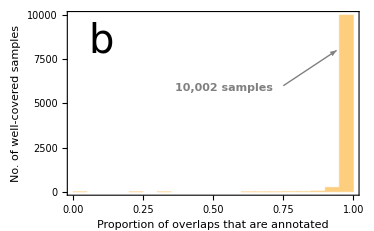

```mathematica
padding={{80,10},{60,12}};fig1b=Show[Histogram[statsBySample[[All,11]]/statsBySample[[All,10]]//N, Frame->True,ImageSize->baseImageSize*.5,BaseStyle->{FontFamily->"Arial",FontSize->15},ImagePadding->padding,FrameLabel->{Style["Proportion of overlaps that are annotated", 15], Style["No. of well-covered samples", 15]}],Graphics[{Gray,Arrow[{{0.75, 6000},{0.94,8000}}],largerLabelForm[ToString[NumberForm[lastBin,DigitBlock->3]]<>" samples", {0.54, 5900}]}],Graphics[{Black, Text[Style["b", FontFamily->"Arial", FontSize->40], {0.1, 8500}]}]]
```

```mathematica
(*junctions by sample*)
```

```mathematica
jxHistList2=HistogramList[statsBySample[[All,7]]/statsBySample[[All,6]]]
```

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1},{1,0,1,1,1,1,18,27,90,132,148,307,474,803,1258,1522,2488,2214,822,3}}

```mathematica
lessThan80=Total[jxHistList2[[2,Range[1,16]]]]
```

4784

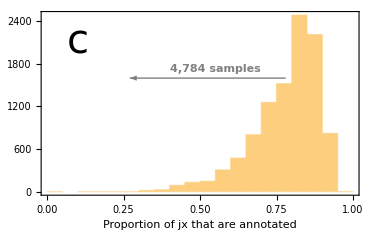

```mathematica
padding2={{75,10},{60,12}};fig1c=Show[Histogram[statsBySample[[All,7]]/statsBySample[[All,6]]//N, Frame->True,ImageSize->baseImageSize*.5,ImagePadding->padding2,BaseStyle->{FontFamily->"Arial",FontSize->15},FrameLabel->{Style["Proportion of jx that are annotated", 15], None}], Graphics[{Gray,Arrow[{{0.78, 1600},{0.27,1600}}], largerLabelForm[ToString[NumberForm[lessThan80,DigitBlock->3]]<>" samples", {0.55, 1730}]}],Graphics[{Black, Text[Style["c", FontFamily->"Arial", FontSize->40], {0.1, 2100}]}]]
```

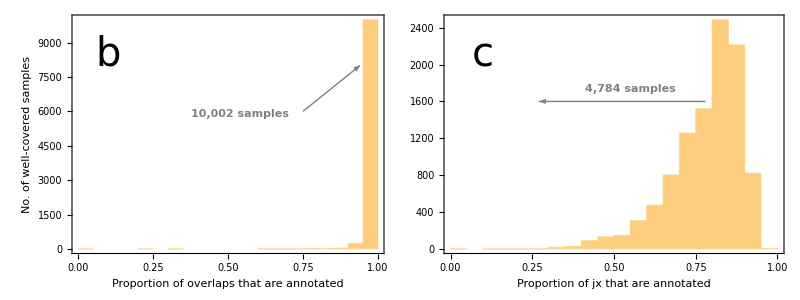
-Graphics-
-Graphics-

```mathematica
fig1=Grid[{{fig1a},{Grid[{{fig1b,fig1c}}]}}]
```

```mathematica
Export["jxannotation.pdf",fig1]
```

jxannotation.pdf

```mathematica
(*SEQC comparison: subset of 1720 samples out of the 21504 that were aligned by SEQC using magic, rmake, subread. Shows that when a junction is in a lot of samples, it's found by other aligners.*)
```

```mathematica
aggregatedJunctionCounts=Drop[Import["hg19.seqc_sample.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];oneAlignerJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
twoAlignerJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,7}]]];
threeAlignerJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,8}]]];
```

```mathematica
totalJunctions[[1710-79]]
```

{80,348531}

```mathematica
idx=1710-79
```

1631

```mathematica
atLeastTwoAlignersJunctions = Transpose[{oneAlignerJunctions[[All,1]],threeAlignerJunctions[[All,2]]+twoAlignerJunctions[[All,2]]}];
atLeastOneAlignerJunctions = Transpose[{oneAlignerJunctions[[All,1]],oneAlignerJunctions[[All,2]]+twoAlignerJunctions[[All,2]]+threeAlignerJunctions[[All,2]]}];
```

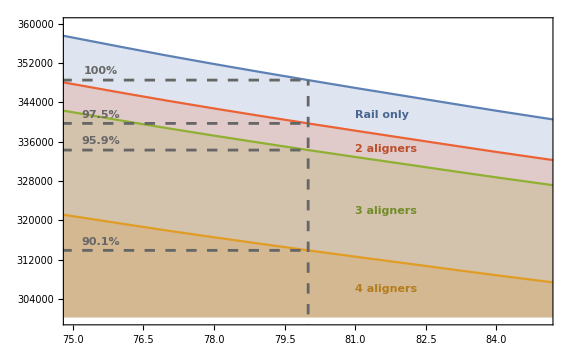

```mathematica
dashedColor=Darker[Gray,0.2];numberStartPos=75.6;insetAnnotationPlot=Show[ListPlot[{totalJunctions,threeAlignerJunctions, atLeastTwoAlignersJunctions, atLeastOneAlignerJunctions}, Joined->True, PlotRange->{{75, 85},{300000,360000}}, Filling->Axis,  Frame->True,ImageSize->Large, BaseStyle->{FontFamily->"Arial",FontSize->15}], Graphics[{Directive[Thickness[0.0035],Dashing[0.013], dashedColor],Line[{{80,0},totalJunctions[[idx]]}],Line[{{0,totalJunctions[[idx]][[2]]},totalJunctions[[idx]]}],Line[{{0,atLeastOneAlignerJunctions[[idx]][[2]]},atLeastOneAlignerJunctions[[idx]]}],
Line[{{0,atLeastTwoAlignersJunctions[[idx]][[2]]},atLeastTwoAlignersJunctions[[idx]]}],Line[{{0,threeAlignerJunctions[[idx]][[2]]},threeAlignerJunctions[[idx]]}],Directive[{Dashing[None],Arrowheads[{-.03,.03}]}], (*Arrow[{{79.63,atLeastOneAlignerJunctions[[idx]][[2]]},{79.63,totalJunctions[[idx]][[2]]}}],bigLabelForm[ToString[NumberForm[N[100-atLeastOneAlignerJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%",{79.5, 345500}, {1,0}],labelForm[ToString[NumberForm[totalJunctions[[idx,2]]-atLeastOneAlignerJunctions[[idx,2]],DigitBlock->3]]<>" jx", {79.5, 341500},{1,0}],*)labelForm["100%",{numberStartPos,totalJunctions[[idx]][[2]]+1800}],labelForm[ToString[NumberForm[N[atLeastOneAlignerJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,atLeastOneAlignerJunctions[[idx]][[2]]+1800}],
labelForm[ToString[NumberForm[N[threeAlignerJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,threeAlignerJunctions[[idx]][[2]]+1800}],
labelForm[ToString[NumberForm[N[atLeastTwoAlignersJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,atLeastTwoAlignersJunctions[[idx]][[2]]+1800}],(*Directive[Thickness[0.0035],Arrowheads[.035],Dashing[None], dashedColor],Arrow[{{1000,totalJunctions[[idx]][[2]]+41000},{1000,totalJunctions[[idx]][[2]]+100}}],labelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100],3]]<>"% of jx unannotated, but\n"<>ToString[NumberForm[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100//N,3]]<>"% of jx have donor and/or\nacceptor site in annotation", {1005, 330000}, {-1,0}],*)Darker[mathematicaColors[[1]], 0.2],labelForm["Rail only",{81,341500}, {-1,0}],Darker[mathematicaColors[[4]], 0.2],labelForm["2 aligners",{81,334500}, {-1,0}],Darker[mathematicaColors[[3]], 0.2],labelForm["3 aligners",{81,322000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2],labelForm["4 aligners",{81,306000}, {-1,0}]}]]
```

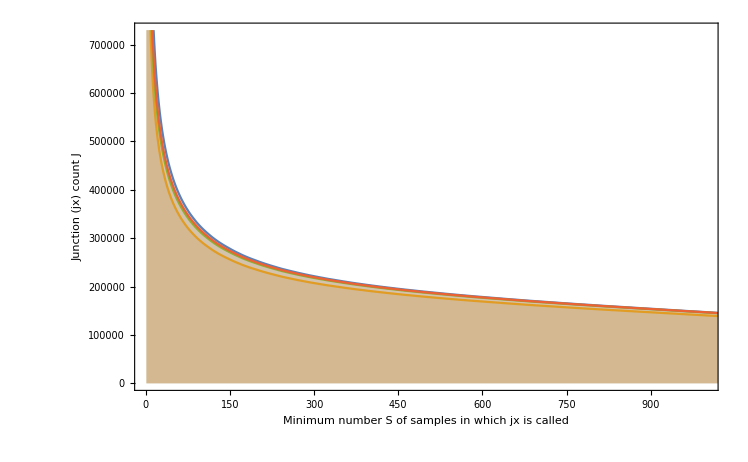

```mathematica
seqcPlot=ListPlot[{totalJunctions,threeAlignerJunctions, atLeastTwoAlignersJunctions,atLeastOneAlignerJunctions}, Joined->True, PlotRange->{{0, 1000},{0,730000}}, Filling->Axis,  Frame->True,ImageSize->baseImageSize, BaseStyle->{FontFamily->"Arial",FontSize->15},Epilog->Inset[insetAnnotationPlot, {625,470000}, Automatic, 700],FrameLabel->{Style["Minimum number S of samples in which jx is called", 22], Style["Junction (jx) count J", 22]}]
```

```mathematica
suppfigseqc=Show[seqcPlot,Graphics[{EdgeForm[Directive[Gray, Thickness[.002]]],Transparent,Rectangle[{75, 300000},{85,360000}]}],Graphics[{Gray,Arrow[{{95,360000},{275,510000}}]}],  Graphics[{Opacity[0.5],Inset[magnifyingGlass,{140,410000},{0,0},50]}],ImageSize->baseImageSize]
```

-Graphics-

```mathematica
Export["seqc.pdf",suppfigseqc]
```

seqc.pdf

```mathematica
(*Repeat Figure 1a, except at project level for supplement*)
```

```mathematica
aggregatedJunctionCounts=Drop[Import["hg19.project.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];annotatedJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,3}]]];exonSkipJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,4}]]];altStartEndJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,5}]]];
novelJunctions=exonSkips=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
```

```mathematica
exonSkipAnnotatedJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]}];
someEvidenceJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]+altStartEndJunctions[[All,2]]}];
```

```mathematica
(*Introduce levels of evidence, and annotated with junction counts for ≥ 30 samples*)
```

```mathematica
totalJunctions[[784-199]]
```

{200,310536}

```mathematica
idx=784-199
```

585

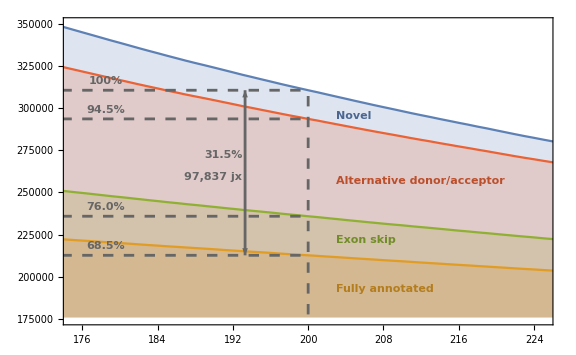

```mathematica
dashedColor=Darker[Gray,0.2];numberStartPos=178.5;insetAnnotationPlot=Show[ListPlot[{totalJunctions,annotatedJunctions,exonSkipAnnotatedJunctions, someEvidenceJunctions}, Joined->True, PlotRange->{{175, 225},{175000,350000}}, Filling->Axis,  Frame->True,ImageSize->Large, BaseStyle->{FontFamily->"Arial",FontSize->15}], Graphics[{Directive[Thickness[0.0035],Dashing[0.013], dashedColor],Line[{{200,0},totalJunctions[[idx]]}],Line[{{0,totalJunctions[[idx]][[2]]},totalJunctions[[idx]]}],Line[{{0,annotatedJunctions[[idx]][[2]]},annotatedJunctions[[idx]]}],
Line[{{0,exonSkipAnnotatedJunctions[[idx]][[2]]},exonSkipAnnotatedJunctions[[idx]]}],Line[{{0,someEvidenceJunctions[[idx]][[2]]},someEvidenceJunctions[[idx]]}],Directive[{Dashing[None],Arrowheads[{-.05,.05}]}], Arrow[{{193.3,annotatedJunctions[[idx]][[2]]},{193.3,totalJunctions[[idx]][[2]]}}],bigLabelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%",{193, 272000}, {1,0}],labelForm[ToString[NumberForm[totalJunctions[[idx,2]]-annotatedJunctions[[idx,2]],DigitBlock->3]]<>" jx", {193, 259000},{1,0}],labelForm["100%",{numberStartPos,totalJunctions[[idx]][[2]]+5300}],labelForm[ToString[NumberForm[N[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,someEvidenceJunctions[[idx]][[2]]+5300}],
labelForm[ToString[NumberForm[N[annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,annotatedJunctions[[idx]][[2]]+5300}],
labelForm[ToString[NumberForm[N[exonSkipAnnotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,exonSkipAnnotatedJunctions[[idx]][[2]]+5300}],Darker[mathematicaColors[[1]], 0.2],labelForm["Novel",{203,295000}, {-1,0}],Darker[mathematicaColors[[4]], 0.2],labelForm["Alternative donor/acceptor",{203,257000}, {-1,0}],Darker[mathematicaColors[[3]], 0.2],labelForm["Exon skip",{203,222000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2],labelForm["Fully annotated",{203,193000}, {-1,0}]}]]
```

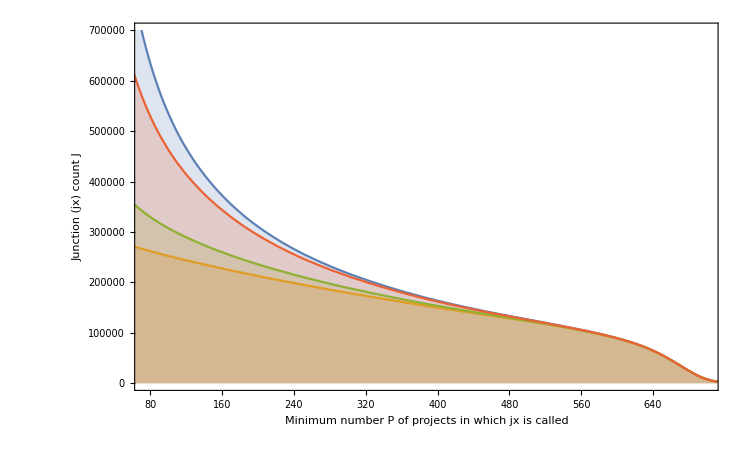

```mathematica
bigAnnotationPlot=ListPlot[{totalJunctions,annotatedJunctions,Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]}], Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]+Transpose[altStartEndJunctions][[2]]}]}, Joined->True, PlotRange->{{75, 700},{0,700000}}, Filling->Axis,  Frame->True,ImageSize->baseImageSize, BaseStyle->{FontFamily->"Arial",FontSize->15},Epilog->Inset[insetAnnotationPlot, {465,440000}, Automatic, 425],FrameLabel->{Style["Minimum number P of projects in which jx is called",22], Style["Junction (jx) count J",22]}]
```

```mathematica
suppfigproj=Show[bigAnnotationPlot,Graphics[{EdgeForm[Directive[Gray, Thickness[.0015]]],Transparent,Rectangle[{175, 175000},{225,350000}]}],Graphics[{Gray,Arrow[{{200,360000},{275,490000}}]}],  Graphics[{Opacity[0.5],Inset[magnifyingGlass,{210,400000},{0,0},30]}],ImageSize->baseImageSize]
```

-Graphics-

```mathematica
Export["projlevel.pdf",suppfigproj]
```

projlevel.pdf

```mathematica
(*For how many runs are we missing Biosample submission dates? We ran the command
cat index_to_SRA_accession.tsv | grep-vwFf <(cat biosample_tags.tsv|cut-f10|tail-n+2)>missing_biosample_dates.tsv
in the sra/hg19 directory of the repo nellore/runs to obtain that dates were missing for only 77/21504=0.3% of runs. Our analysis is reasonably complete if we ignore them.*)
```

```mathematica
junctionsEvidenceVsDatesGeq20=Drop[Import["!gzip -cd hg19.sample_count_submission_date_overlap_geq_20.tsv.gz", "TSV"], 1];
```

$Aborted

```mathematica
junctionsEvidenceVsDatesGeq[x_]:= Select[junctionsEvidenceVsDatesGeq20,#[[1]]≥x &];talliedJunctionsGeq[x_]:=SortBy[Tally[junctionsEvidenceVsDatesGeq[x][[All,4]]], First];accumulatedJunctionsGeq[x_]:=(talliedJunctions=talliedJunctionsGeq[x];Transpose[{talliedJunctions[[All,1]],Accumulate[talliedJunctions[[All,2]]]}])
```

```mathematica
(*Convert from days after 2/27/2009 to dates*)
```

```mathematica
daysToDate = DateObject[{2009, 2, 27}]+LinguisticAssistant &
```

Fri 27 Feb 2009+#1&

```mathematica
(*When were junctions supported by reads in ≥ 20, 40, 80, 160 reads across samples found?*)
```

```mathematica
twentyThirteen=1404;daysToDate[twentyThirteen]
```

Tue 1 Jan 2013

```mathematica
dateFormat={"Month","/","Day","/","YearShort"};
```

```mathematica
(*Design ticks to intersect 1/1/2013*)
```

```mathematica
dateTicks=({#,DateString[daysToDate[#], dateFormat]}&/@Range[0, 2070, 234])
```

{{0,02/27/09},{234,10/19/09},{468,06/10/10},{702,01/30/11},{936,09/21/11},{1170,05/12/12},{1404,01/01/13},{1638,08/23/13},{1872,04/14/14}}

```mathematica
lastDay=Max[junctionsEvidenceVsDatesGeq20[[All,4]]]
```

2070

```mathematica
dateTicks=Append[dateTicks, {lastDay,DateString[daysToDate[lastDay], dateFormat]}]
```

{{0,02/27/09},{234,10/19/09},{468,06/10/10},{702,01/30/11},{936,09/21/11},{1170,05/12/12},{1404,01/01/13},{1638,08/23/13},{1872,04/14/14},{2070,10/29/14}}

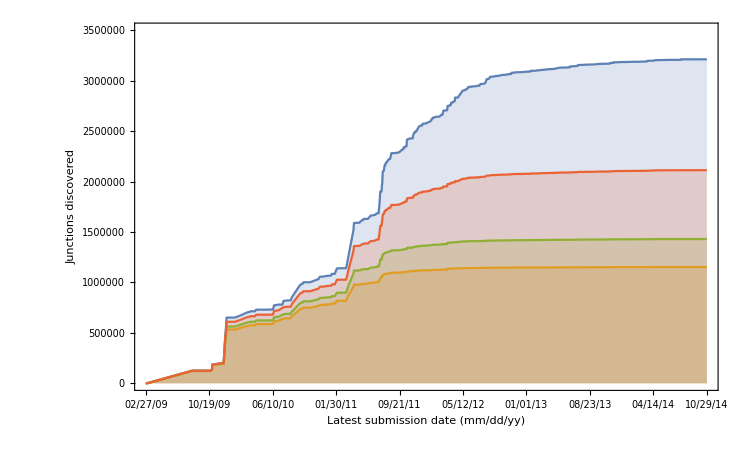

```mathematica
baseJunctionsPlot=ListPlot[accumulatedJunctionsGeq/@{20,120, 80,40}, Joined->True,Filling->Axis, Frame->True, FrameTicks->{{Automatic,None},{dateTicks, None}},BaseStyle->{FontFamily->"Arial",FontSize->14}, FrameLabel->{Style["Latest submission date (mm/dd/yy)", 22], Style["Junctions discovered", 22]}, ImageSize->baseImageSize, PlotRange->{All, {0, 3.5*10^6}}]
```

```mathematica
sortedDays= Sort[junctionsEvidenceVsDates[[All,3]]];
```

```mathematica
junctionsInCommons=Count[sortedDays, #]&/@Commonest[sortedDays,7]
```

{123759,124121,155069,163007,124664,252628,162196}

```mathematica
(*These correspond to, respectively....*)
```

```mathematica
daysToDate/@Commonest[sortedDays,7]
```

{Sun 16 Aug 2009,Mon 14 Dec 2009,Thu 17 Dec 2009,Tue 22 Dec 2009,Thu 17 Mar 2011,Mon 4 Apr 2011,Tue 12 Jul 2011}

```mathematica
(*Some of these dates correspond to jumps in the plot above. Grepping for the submission dates in biosample_tags.tsv in sra/hg19 gives samples in the following projects:
1. who cares
2. who cares
3. Study of 69 LCLs (2)(Understanding mechanisms underlying human gene expression variation with RNA sequencing, by Pickrell et al.) (SRP001540) 17 Dec 2009
4. Study of 41 Coriell cell lines (SRP001563)(Polymorphic cis-and trans-regulation of human gene expression, by Cheung et al.) 22 Dec 2009
5. Illumina bodyMap2 (ERP000546) 17-Mar-2011
6. University of Washington Human Reference Epigenome Mapping Project (SRP001371)(total RNA, fetal tissues, contributed most junctions on a single day (4 April 2011)); note also that on this day, there are two more projects: SRP005309, a microRNA study with negligible # junctions, and SRP005846, for which grepping hg19.stats_by_sample.tsv gives ~95 annotated jx, < 50k each of 4 samples. So overwhelmingly dominant contribution on 4 April 2011 is UW.
7. ENCODE long RNA-seq from CSHL (SRP007461) 12-Jul-2011

Annotate plot with the top 4 projects (3,4,6, and 7 above); the 1st, 2nd, and 5th are about the same size but have many fewer junctions than the top 4 contributors

Find GEUVADIS. Grepping biosample_tags.tsv gives that the GEUVADIS submission date was 2012-11-07. This was 
*)
```

```mathematica
daysToDate[1349]
```

Wed 7 Nov 2012

```mathematica
(*A glance at the tallies below shows that just 11294 novel junctions were contributed on the day GEUVADIS samples were submitted to Biosample! *)
```

```mathematica
tallied=Tally[sortedDays]
```

{{0,1110},{7,624},{170,123759},{213,70},{237,55},{244,10389},{245,50729},{278,13334},{287,9},{290,124121},{293,155069},{294,9318},{298,163007},{329,50},{356,28624},{362,8285},{376,15841},{382,2878},{388,6900},{398,10},{403,72},{406,14113},{411,1632},{418,42},{448,214},{454,582},{469,1429},{473,40933},{474,15},{490,7270},{504,1},{508,36019},{511,5},{515,3186},{525,1521},{535,1267},{538,27738},{566,112496},{573,21129},{578,695},{581,17055},{606,49},{637,31778},{642,22678},{648,1386},{654,35},{671,8394},{677,434},{679,790},{684,2408},{686,15188},{697,26},{705,54568},{718,692},{739,1470},{748,124664},{766,252628},{768,70376},{788,2783},{791,8257},{795,10214},{798,6030},{801,1370},{803,10521},{819,1655},{824,14227},{829,17430},{837,3048},{847,5902},{851,14186},{859,904},{860,47163},{861,5641},{865,162196},{870,1600},{871,67018},{872,1659},{874,123474},{877,11239},{878,268},{881,54855},{882,2501},{884,819},{885,18340},{886,4513},{889,2528},{896,31640},{901,548},{906,59520},{910,86},{921,1682},{930,3243},{935,3954},{936,1},{937,5905},{943,14686},{945,1035},{950,11778},{951,337},{952,16763},{956,566},{959,5763},{962,3082},{963,57275},{965,11806},{969,594},{970,943},{971,1358},{972,3666},{974,1507},{985,462},{986,27558},{990,28199},{993,1969},{994,11304},{998,70},{1007,44673},{1008,3680},{1011,6130},{1014,2180},{1015,86},{1018,657},{1019,701},{1021,15130},{1022,3414},{1033,1845},{1035,1188},{1036,3752},{1043,7398},{1047,5465},{1049,3837},{1053,5246},{1054,12145},{1055,6846},{1056,3},{1057,1475},{1059,8659},{1060,26},{1061,3282},{1067,946},{1069,6340},{1070,4},{1081,519},{1083,1},{1084,686},{1089,16982},{1092,1},{1095,2970},{1096,19603},{1097,9063},{1098,10301},{1099,1719},{1102,4},{1104,396},{1106,193},{1109,4},{1112,3385},{1113,40568},{1116,455},{1118,942},{1119,3927},{1120,869},{1124,596},{1125,1235},{1126,23732},{1129,3015},{1132,100},{1133,69},{1134,7020},{1140,7364},{1141,34226},{1146,92},{1151,259},{1166,57205},{1169,11585},{1174,1557},{1175,663},{1180,7802},{1181,420},{1182,4},{1183,4788},{1188,10953},{1189,204},{1190,9213},{1193,123},{1194,34},{1195,2713},{1197,200},{1200,206},{1202,146},{1207,2681},{1208,398},{1209,338},{1214,19},{1215,42},{1222,4291},{1224,528},{1225,378},{1228,1},{1230,243},{1231,65},{1232,11969},{1236,5507},{1238,24},{1239,500},{1242,210},{1243,860},{1244,19},{1245,893},{1250,2128},{1253,8601},{1257,30849},{1258,3488},{1263,3301},{1264,515},{1265,211},{1267,3047},{1270,16862},{1277,651},{1279,20},{1281,1433},{1285,1131},{1286,5},{1287,552},{1288,2187},{1289,97},{1290,219},{1291,205},{1292,111},{1293,5},{1294,72},{1295,2060},{1296,29},{1299,40},{1300,818},{1301,1947},{1302,45},{1305,61},{1307,196},{1308,326},{1309,255},{1313,5697},{1315,109},{1316,383},{1321,316},{1326,864},{1327,252},{1330,1712},{1333,659},{1334,1000},{1335,189},{1337,1451},{1339,1613},{1340,22},{1344,37},{1348,961},{1349,11294},{1350,142},{1351,1460},{1352,33},{1357,494},{1361,301},{1362,1604},{1364,1204},{1365,132},{1369,1},{1370,29},{1371,445},{1372,115},{1376,229},{1379,455},{1386,156},{1387,212},{1388,59},{1389,70},{1392,68},{1393,2766},{1398,188},{1399,2},{1400,293},{1405,676},{1406,13},{1407,463},{1410,330},{1411,87},{1417,70},{1418,936},{1419,19},{1420,6790},{1421,2},{1425,39},{1431,625},{1433,28},{1439,400},{1443,3072},{1446,25},{1447,692},{1452,1233},{1453,42},{1456,344},{1459,2966},{1461,116},{1463,16},{1469,626},{1475,2617},{1476,277},{1477,40},{1480,842},{1482,1675},{1484,543},{1485,7},{1487,160},{1488,177},{1492,2},{1495,329},{1496,783},{1497,27},{1498,56},{1501,29},{1502,1028},{1503,632},{1508,174},{1510,136},{1512,1857},{1516,5111},{1518,954},{1522,911},{1523,405},{1524,633},{1526,1298},{1529,743},{1531,23},{1533,56},{1537,1},{1539,493},{1540,116},{1543,191},{1545,127},{1546,15},{1551,175},{1552,427},{1553,12},{1556,241},{1557,413},{1558,246},{1559,62},{1560,191},{1561,559},{1564,68},{1565,7893},{1567,304},{1568,87},{1571,1651},{1574,26},{1575,127},{1578,63},{1579,1071},{1580,53},{1581,78},{1582,589},{1585,27},{1586,16},{1587,499},{1588,11},{1589,1},{1592,2609},{1594,37},{1595,7294},{1596,299},{1597,263},{1599,364},{1600,87},{1603,12},{1606,11},{1607,289},{1610,25},{1612,6},{1613,199},{1614,194},{1615,47},{1617,79},{1621,854},{1622,174},{1623,1005},{1627,21},{1628,1},{1629,116},{1633,2},{1634,119},{1636,590},{1642,42},{1643,279},{1644,1},{1645,366},{1646,24},{1648,7},{1649,105},{1650,282},{1651,20},{1655,30},{1656,218},{1657,920},{1660,59},{1663,899},{1665,1533},{1670,911},{1671,16},{1672,4},{1673,731},{1676,39},{1678,864},{1693,2},{1694,270},{1697,578},{1699,6},{1701,367},{1704,7},{1705,8},{1707,15},{1708,31},{1711,1},{1712,1981},{1713,125},{1714,5338},{1715,190},{1718,54},{1719,1},{1721,54},{1722,41},{1725,74},{1726,5625},{1728,282},{1729,202},{1730,4},{1733,34},{1740,3},{1741,9},{1743,35},{1744,1355},{1747,360},{1748,227},{1750,21},{1753,10},{1755,82},{1756,52},{1757,96},{1760,6},{1761,71},{1763,166},{1767,471},{1776,133},{1777,1},{1778,18},{1781,92},{1782,811},{1783,36},{1784,106},{1787,5},{1790,3},{1791,11},{1792,311},{1795,19},{1796,329},{1797,12},{1799,14},{1805,37},{1806,172},{1810,14},{1811,40},{1813,4},{1817,1},{1818,8},{1819,5},{1820,14},{1822,4},{1823,42},{1824,14},{1825,1383},{1830,35},{1831,9},{1837,129},{1838,59},{1840,1037},{1841,79},{1842,2},{1844,8},{1846,126},{1847,44},{1849,835},{1850,3305},{1851,2376},{1852,9},{1853,242},{1854,20},{1855,6},{1859,96},{1860,336},{1861,13},{1862,10},{1865,60},{1866,43},{1867,13},{1868,44},{1869,1},{1872,23},{1873,19},{1874,15},{1875,14},{1880,5724},{1881,26},{1884,9},{1886,1},{1889,7},{1890,1},{1894,23},{1895,42},{1896,94},{1897,7},{1900,3},{1901,3},{1902,7},{1904,302},{1908,4},{1909,495},{1910,183},{1915,176},{1918,2},{1921,707},{1928,2},{1929,6},{1930,266},{1931,13},{1933,92},{1937,9},{1938,7},{1949,5},{1950,3},{1958,1},{1960,3},{1966,62},{1967,1},{1970,36},{1974,3},{1975,5140},{1977,1},{1993,6},{2010,1},{2014,1},{2029,9},{2070,358}}

```mathematica
(*Find GEUV day's rank: *)
```

```mathematica
Reverse[SortBy[tallied, Last]]
```

{{766,252628},{298,163007},{865,162196},{293,155069},{748,124664},{290,124121},{170,123759},{874,123474},{566,112496},{768,70376},{871,67018},{906,59520},{963,57275},{1166,57205},{881,54855},{705,54568},{245,50729},{860,47163},{1007,44673},{473,40933},{1113,40568},{508,36019},{1141,34226},{637,31778},{896,31640},{1257,30849},{356,28624},{990,28199},{538,27738},{986,27558},{1126,23732},{642,22678},{573,21129},{1096,19603},{885,18340},{829,17430},{581,17055},{1089,16982},{1270,16862},{952,16763},{376,15841},{686,15188},{1021,15130},{943,14686},{824,14227},{851,14186},{406,14113},{278,13334},{1054,12145},{1232,11969},{965,11806},{950,11778},{1169,11585},{994,11304},{1349,11294},{877,11239},{1188,10953},{803,10521},{244,10389},{1098,10301},{795,10214},{294,9318},{1190,9213},{1097,9063},{1059,8659},{1253,8601},{671,8394},{362,8285},{791,8257},{1565,7893},{1180,7802},{1043,7398},{1140,7364},{1595,7294},{490,7270},{1134,7020},{388,6900},{1055,6846},{1420,6790},{1069,6340},{1011,6130},{798,6030},{937,5905},{847,5902},{959,5763},{1880,5724},{1313,5697},{861,5641},{1726,5625},{1236,5507},{1047,5465},{1714,5338},{1053,5246},{1975,5140},{1516,5111},{1183,4788},{886,4513},{1222,4291},{935,3954},{1119,3927},{1049,3837},{1036,3752},{1008,3680},{972,3666},{1258,3488},{1022,3414},{1112,3385},{1850,3305},{1263,3301},{1061,3282},{930,3243},{515,3186},{962,3082},{1443,3072},{837,3048},{1267,3047},{1129,3015},{1095,2970},{1459,2966},{382,2878},{788,2783},{1393,2766},{1195,2713},{1207,2681},{1475,2617},{1592,2609},{889,2528},{882,2501},{684,2408},{1851,2376},{1288,2187},{1014,2180},{1250,2128},{1295,2060},{1712,1981},{993,1969},{1301,1947},{1512,1857},{1033,1845},{1099,1719},{1330,1712},{921,1682},{1482,1675},{872,1659},{819,1655},{1571,1651},{411,1632},{1339,1613},{1362,1604},{870,1600},{1174,1557},{1665,1533},{525,1521},{974,1507},{1057,1475},{739,1470},{1351,1460},{1337,1451},{1281,1433},{469,1429},{648,1386},{1825,1383},{801,1370},{971,1358},{1744,1355},{1526,1298},{535,1267},{1125,1235},{1452,1233},{1364,1204},{1035,1188},{1285,1131},{0,1110},{1579,1071},{1840,1037},{945,1035},{1502,1028},{1623,1005},{1334,1000},{1348,961},{1518,954},{1067,946},{970,943},{1118,942},{1418,936},{1657,920},{1670,911},{1522,911},{859,904},{1663,899},{1245,893},{1120,869},{1678,864},{1326,864},{1243,860},{1621,854},{1480,842},{1849,835},{884,819},{1300,818},{1782,811},{679,790},{1496,783},{1529,743},{1673,731},{1921,707},{1019,701},{578,695},{1447,692},{718,692},{1084,686},{1405,676},{1175,663},{1333,659},{1018,657},{1277,651},{1524,633},{1503,632},{1469,626},{1431,625},{7,624},{1124,596},{969,594},{1636,590},{1582,589},{454,582},{1697,578},{956,566},{1561,559},{1287,552},{901,548},{1484,543},{1224,528},{1081,519},{1264,515},{1239,500},{1587,499},{1909,495},{1357,494},{1539,493},{1767,471},{1407,463},{985,462},{1379,455},{1116,455},{1371,445},{677,434},{1552,427},{1181,420},{1557,413},{1523,405},{1439,400},{1208,398},{1104,396},{1316,383},{1225,378},{1701,367},{1645,366},{1599,364},{1747,360},{2070,358},{1456,344},{1209,338},{951,337},{1860,336},{1410,330},{1796,329},{1495,329},{1308,326},{1321,316},{1792,311},{1567,304},{1904,302},{1361,301},{1596,299},{1400,293},{1607,289},{1728,282},{1650,282},{1643,279},{1476,277},{1694,270},{878,268},{1930,266},{1597,263},{1151,259},{1309,255},{1327,252},{1558,246},{1230,243},{1853,242},{1556,241},{1376,229},{1748,227},{1290,219},{1656,218},{448,214},{1387,212},{1265,211},{1242,210},{1200,206},{1291,205},{1189,204},{1729,202},{1197,200},{1613,199},{1307,196},{1614,194},{1106,193},{1560,191},{1543,191},{1715,190},{1335,189},{1398,188},{1910,183},{1488,177},{1915,176},{1551,175},{1622,174},{1508,174},{1806,172},{1763,166},{1487,160},{1386,156},{1202,146},{1350,142},{1510,136},{1776,133},{1365,132},{1837,129},{1575,127},{1545,127},{1846,126},{1713,125},{1193,123},{1634,119},{1629,116},{1540,116},{1461,116},{1372,115},{1292,111},{1315,109},{1784,106},{1649,105},{1132,100},{1289,97},{1859,96},{1757,96},{1896,94},{1933,92},{1781,92},{1146,92},{1600,87},{1568,87},{1411,87},{1015,86},{910,86},{1755,82},{1841,79},{1617,79},{1581,78},{1725,74},{1294,72},{403,72},{1761,71},{1417,70},{1389,70},{998,70},{213,70},{1133,69},{1564,68},{1392,68},{1231,65},{1578,63},{1966,62},{1559,62},{1305,61},{1865,60},{1838,59},{1660,59},{1388,59},{1533,56},{1498,56},{237,55},{1721,54},{1718,54},{1580,53},{1756,52},{329,50},{606,49},{1615,47},{1302,45},{1868,44},{1847,44},{1866,43},{1895,42},{1823,42},{1642,42},{1453,42},{1215,42},{418,42},{1722,41},{1811,40},{1477,40},{1299,40},{1676,39},{1425,39},{1805,37},{1594,37},{1344,37},{1970,36},{1783,36},{1830,35},{1743,35},{654,35},{1733,34},{1194,34},{1352,33},{1708,31},{1655,30},{1501,29},{1370,29},{1296,29},{1433,28},{1585,27},{1497,27},{1881,26},{1574,26},{1060,26},{697,26},{1610,25},{1446,25},{1646,24},{1238,24},{1894,23},{1872,23},{1531,23},{1340,22},{1750,21},{1627,21},{1854,20},{1651,20},{1279,20},{1873,19},{1795,19},{1419,19},{1244,19},{1214,19},{1778,18},{1671,16},{1586,16},{1463,16},{1874,15},{1707,15},{1546,15},{474,15},{1875,14},{1824,14},{1820,14},{1810,14},{1799,14},{1931,13},{1867,13},{1861,13},{1406,13},{1797,12},{1603,12},{1553,12},{1791,11},{1606,11},{1588,11},{1862,10},{1753,10},{398,10},{2029,9},{1937,9},{1884,9},{1852,9},{1831,9},{1741,9},{287,9},{1844,8},{1818,8},{1705,8},{1938,7},{1902,7},{1897,7},{1889,7},{1704,7},{1648,7},{1485,7},{1993,6},{1929,6},{1855,6},{1760,6},{1699,6},{1612,6},{1949,5},{1819,5},{1787,5},{1293,5},{1286,5},{511,5},{1908,4},{1822,4},{1813,4},{1730,4},{1672,4},{1182,4},{1109,4},{1102,4},{1070,4},{1974,3},{1960,3},{1950,3},{1901,3},{1900,3},{1790,3},{1740,3},{1056,3},{1928,2},{1918,2},{1842,2},{1693,2},{1633,2},{1492,2},{1421,2},{1399,2},{2014,1},{2010,1},{1977,1},{1967,1},{1958,1},{1890,1},{1886,1},{1869,1},{1817,1},{1777,1},{1719,1},{1711,1},{1644,1},{1628,1},{1589,1},{1537,1},{1369,1},{1228,1},{1092,1},{1083,1},{936,1},{504,1}}

```mathematica
Position[Reverse[SortBy[tallied, Last]],{1349,11294}]
```

{{55}}

```mathematica
(*GEUV is at 55!*)
```

```mathematica
geuvDate=1349
```

1349

```mathematica
junctionsInCommons=Count[sortedDays, #]&/@Commonest[sortedDays,30]
```

{123759,50729,124121,155069,163007,28624,40933,36019,27738,112496,31778,54568,124664,252628,70376,47163,162196,67018,123474,54855,31640,59520,57275,27558,28199,44673,40568,34226,57205,30849}

```mathematica
daysToDate/@Commonest[sortedDays,30]
```

{Sun 16 Aug 2009,Fri 30 Oct 2009,Mon 14 Dec 2009,Thu 17 Dec 2009,Tue 22 Dec 2009,Thu 18 Feb 2010,Tue 15 Jun 2010,Tue 20 Jul 2010,Thu 19 Aug 2010,Thu 16 Sep 2010,Fri 26 Nov 2010,Wed 2 Feb 2011,Thu 17 Mar 2011,Mon 4 Apr 2011,Wed 6 Apr 2011,Thu 7 Jul 2011,Tue 12 Jul 2011,Mon 18 Jul 2011,Thu 21 Jul 2011,Thu 28 Jul 2011,Fri 12 Aug 2011,Mon 22 Aug 2011,Tue 18 Oct 2011,Thu 10 Nov 2011,Mon 14 Nov 2011,Thu 1 Dec 2011,Fri 16 Mar 2012,Fri 13 Apr 2012,Tue 8 May 2012,Tue 7 Aug 2012}

```mathematica
arrowLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.03],Bold,TextAlignment->Left], y]
```

```mathematica
altLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.045],Bold,TextAlignment->Left], y]
```

```mathematica
accJunc=accumulatedJunctionsGeq[20];
```

```mathematica
maxAtTwentyThirteen=Select[accJunc, #[[1]]<=twentyThirteen &][[-1]][[2]]
```

3087471

```mathematica
maxAtEnd=accJunc[[-1]][[2]]
```

3211228

```mathematica
(*How many junctions covered by ≥ 20 reads are there?*)
```

```mathematica
Length[junctionsEvidenceVsDates]
```

3211228

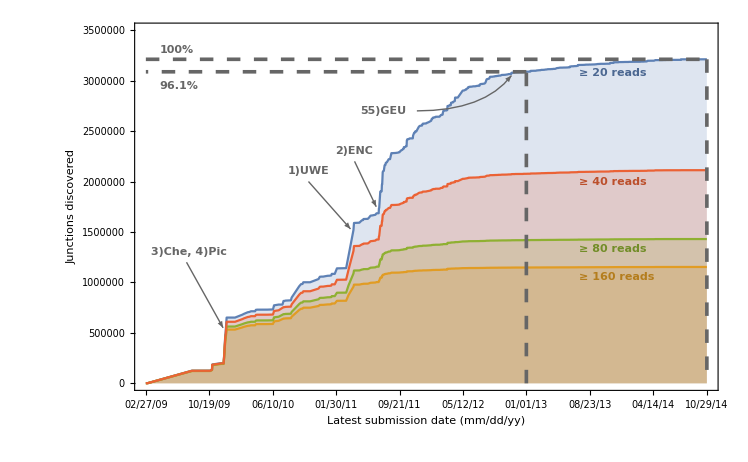

```mathematica
labelColor=Darker[Gray,0.2];leftPos=1600;fig2=Show[baseJunctionsPlot, Graphics[{labelColor,Arrow[{{150,1.2*10^6},{285,550000}}],arrowLabelForm["3)Che, 4)Pic", {160,1.3*10^6}],Arrow[{{600,2*10^6},{755,1.53*10^6}}],arrowLabelForm["1)UWE", {600,2.1*10^6}],Arrow[{{770,2.2*10^6},{850,1.75*10^6}}],Arrow[BezierCurve[{{1000,2.7*10^6},{1249,2.7*10^6},{1349,3.05*10^6}}]],arrowLabelForm["2)ENC", {770,2.3*10^6}], Directive[Thickness[0.0035],Dashing[0.013], labelColor],arrowLabelForm["55)GEU", {875,2.7*10^6}], Directive[Thickness[0.0035],Dashing[0.013], labelColor],Line[{{twentyThirteen,0},{twentyThirteen,maxAtTwentyThirteen}}],Line[{{twentyThirteen,maxAtTwentyThirteen},{0,maxAtTwentyThirteen}}],Line[{{lastDay,maxAtEnd},{lastDay,0}}],Line[{{0,maxAtEnd},{lastDay,maxAtEnd}}],arrowLabelForm["100%", {50, 3.3*10^6}, {-1,0}],altLabelForm[ToString[NumberForm[N[maxAtTwentyThirteen/maxAtEnd*100,3],DigitBlock->3]]<>"%", {50, 2.95*10^6}, {-1,0}],Darker[mathematicaColors[[2]],0.2],arrowLabelForm["≥ 160 reads", {leftPos, 1.055*10^6}, {-1,0}],Darker[mathematicaColors[[3]],0.2],arrowLabelForm["≥ 80 reads", {leftPos, 1.33*10^6}, {-1,0}],Darker[mathematicaColors[[4]],0.2],arrowLabelForm["≥ 40 reads", {leftPos, 2*10^6}, {-1,0}],Darker[mathematicaColors[[1]],0.2],arrowLabelForm["≥ 20 reads", {leftPos,  3.06*10^6}, {-1,0}]}]]
```

```mathematica
Export["dateplot.pdf", fig2]
```

dateplot.pdf